# Weighted fiber + GRIN

-Graphics-

[1] L. Huo, J. Xi, Y. Wu, and X. Li, “Forward-viewing resonant fiber-optic scanning endoscope of appropriate scanning speed for 3D OCT imaging.,” Opt. Express, vol. 18, no. 14, pp. 14375–14384, 2010.

Note: The scanner is approximated to be a fiber connected to a rigid metallic cylinder!

### Input Parameters

```mathematica
LGRIN = 2.08*10^-3;  (*[m] Length of GRIN lens*)
DGRIN = 0.35*10^-3;  (*[m] Diameter of GRIN lens *)
```

```mathematica
(*Ltot = 4.5*10^-3; *) (*[m] Total Length of the scanning tip: fiber + GRIN*)
```

### Calculation of resonant frequency

```mathematica
freqs1 = Table[
D1 = 80*10^-6;  (*[m]*)
ρ1 = 2203; (*[kg/m^3]*) (*seibel2006*)
E1 = 73.1*10^9; (*[Pa]*) (*seibel2006*)
A1 = (D1/2)^2*π;
I1 = π/4*(D1/2)^4; (*[m^4]*)
L1 = Ltot-LGRIN;
D2 = DGRIN;
ρ2 = 2203; (*[kg/m^3]*) 
E2 = 73.1*10^9; (*[Pa]*) 
A2 = (D2/2)^2*π;
I2 = π/4*(D2/2)^4; (*[m^4]*)
L2 = LGRIN;
k1 = √(((ρ1*A1)/(E1*I1))^(1/2)*ω);
k2 = √(((ρ2*A2)/(E2*I2))^(1/2)*ω);
q1 = k1*L1;
q2 = k2*L2;
mat={{Sin[q1]-Sinh[q1],Cos[q1]-Cosh[q1],-Sin[q2]-Sinh[q2],-Cos[q2]-Cosh[q2]},
         {Cos[q1]-Cosh[q1],-Sin[q1]-Sinh[q1],k2/k1*(Cos[q2]+Cosh[q2]),k2/k1*(Sinh[q2]-Sin[q2])},
        {-Sin[q1]-Sinh[q1],-Cos[q1]-Cosh[q1],(k2/k1)^2*I2/I1*(Sin[q2]-Sinh[q2]),(k2/k1)^2*I2/I1*(Cos[q2]-Cosh[q2])},
        {-Cos[q1]-Cosh[q1],Sin[q1]-Sinh[q1],(k2/k1)^3*I2/I1*(Cosh[q2]-Cos[q2]),(k2/k1)^3*I2/I1*(Sin[q2]+Sinh[q2])}};
f = (ω/.FindRoot[Det[mat]==0,{ω,1000}])/(2π)
,{Ltot,3*10^-3,10*10^-3,0.1*10^-3}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

### Minimum Weighted Frequency

```mathematica
fmin = Min[freqs]
```

187.668

### Plot Results

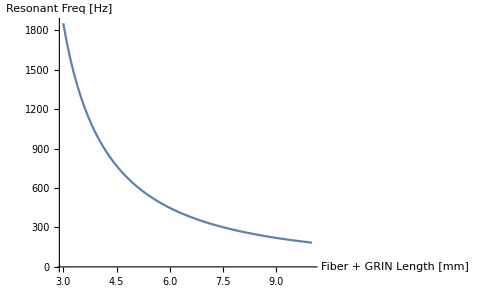

```mathematica
l= Range[3,10,0.1];
ListLinePlot[Thread[{l,freqs1}],PlotRange->Automatic,AxesLabel->{"Fiber + GRIN Length [mm]","Resonant Freq [Hz]"}]
```

### Approximated Resonant Frequency

Asuming concentrated load in the center of gravity of the GRIN lens:

```mathematica
freqs2 = Table[
L1 = Ltot-LGRIN/2;
L2 = LGRIN;
kcant = (3π)/4*(E1*(D1/2)^4)/L1^3;
weight = ρ2*(D2/2)^2*π*L2;
f = 1/(2π)√(kcant/weight)
,{Ltot,3*10^-3,10*10^-3,0.1*10^-3}];
```

```mathematica
l= Range[3,10,0.1];
```

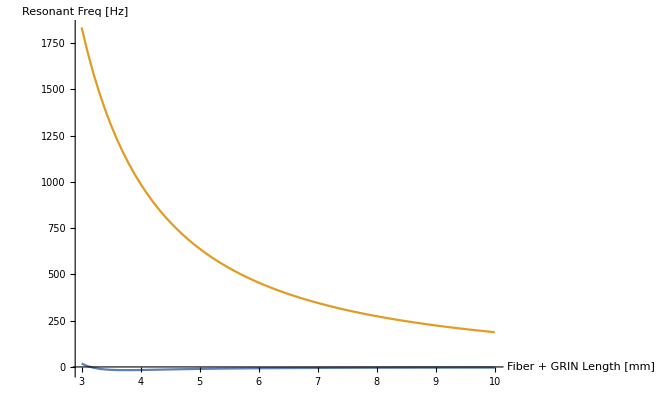

```mathematica
ListLinePlot[{Thread[{l,freqs1-freqs2}],Thread[{l,freqs2}]},PlotRange->Automatic,AxesLabel->{"Fiber + GRIN Length [mm]","Resonant Freq [Hz]"}]
```

### Deflection due to gravity

Asuming concentrated load at the end of L1: Only valid for small coverage factor!!!

```mathematica
deflections = Table[
L1 = L;
L2 = LGRIN;
kcant = (3π)/4*(E1*(D1/2)^4)/L1^3;
weight = ρ2*(D2/2)^2*π*L2;
Δx = (weight*9.8)/kcant

,{L,0,10*10^-3,0.1*10^-3}];
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
ListLinePlot[Thread[{perc,deflections}],PlotRange->Automatic,AxesLabel->{"Length of fiber","Tip deflection [m]"}]
```

-Graphics-

### Bending Beam

```mathematica
length = L-;
Cd = 100*10^-6;
```

```mathematica
k1=1.875; (*meinert2013*)
bendingLine[x_,L_]:=-Cd*(Cos[k1*x/L]-Cosh[k1*x/L]-0.734*(Sin[k1*x/L]-Sinh[k1*x/L]));
```

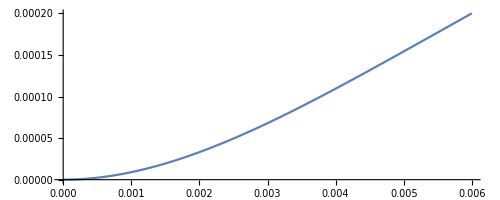

```mathematica
Plot[{bendingLine[x,length]},{x,0,length},AspectRatio->Automatic]
```

```mathematica
angle[x_,L_]:=(180/π)*ArcTan[D[bendingLine[x,length],x]];
```

```mathematica
tipAngle=angle[x,length]/.{x->length}
```

2.62756